# PHAS2443: Practical Mathematics II Exercises 2: Convolutions and Images

1. This exercise explores the accuracy of approximations to derivatives. Look at the three functions
   a)   Exp[-x]
   b)  Sin[x]
   c)  Log[x]
   and consider their derivatives in the range 0.01<x<2π.
   For each function use graphs to compare 
   i) the exact derivative
   ii) the 'forward difference' approximation, df/dt≈(f(t+δt)-f(t))/δt
   iii) the 'backward difference' approximation, df/dt≈(f(t)-f(t-δt))/δt
   iv) the 'centred difference' approximation,  df/dt≈(f(t+δt)-f(t-δt))/(2 δt).
   Try to use efficient methods for implementing the derivatives.
   Experiment with various values of the finite difference, δt.  Can you draw any general conclusions about the relative accuracies of the one-sided and centred differences?

### Exp[-x]

0.2

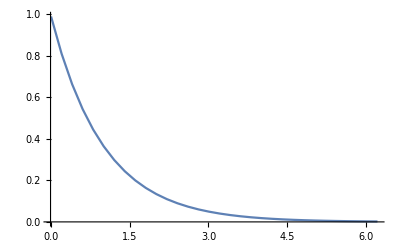

```mathematica
del = 0.2
expList = Table[{x, Exp[-x]}, {x, 0.01, 2π, del}]; (** table of {x,y} values for Exp[-x] with 0.01 < x <2π **)
ListPlot[expList, Joined -> True]
```

### List rotation method

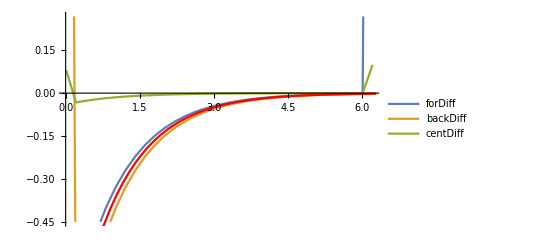

```mathematica
{expX, expY} = Transpose[expList]; (** separate the x & y coords into separate lists **)

forDiff = Transpose[{expX, (RotateLeft[expY] - expY) / del}];
backDiff = Transpose[{expX, (expY - RotateRight[expY]) / del}];
centDiff = Transpose[{expX, (RotateLeft[expY] - RotateRight[expY]) / 2 del}];

listExp = ListPlot[{forDiff, backDiff, centDiff}, Joined -> True, PlotLegends -> {"forDiff", "backDiff", "centDiff"}];
exactExp = Plot[D[Exp[-x], x]/.x->t, {t, 0.01, 2π}, PlotStyle -> Red, PlotLegends -> "Exact"] ;
Show[listExp, exactExp]
```

### List convolution method

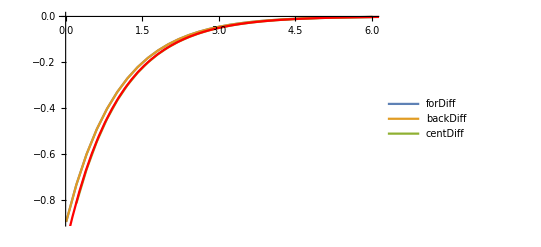

```mathematica
forDiffConv = 
Transpose[
{
Drop[expX, -1], (** drop the first value as ListConvolve drops a value **)
ListConvolve[
{1/ del, -1/del}, expY]
} 
];

backDiffConv = 
Transpose[
{
Drop[expX, -1], 
Drop[
ListConvolve[
{1/ del, -1/del},
 expY,
 1 (** change the index, drop the first value later **)
],
1]
}
];

centDiffConv = 
Transpose[
{
Drop[Drop[expX, -1], 1], (** ListConvolve drops the first and last value **)
ListConvolve[
{1/(2del), 0,-1/(2del)},
expY
]
}
];

listExpConv = ListPlot[{forDiffConv, backDiffConv, centDiffConv}, Joined -> True, PlotLegends -> {"forDiff", "backDiff", "centDiff"}];
Show[listExpConv, exactExp]
```

2. This problem involves setting up a simple one-dimensional model of diffusion. Imagine that space is divided up into a finite number of positions, and that on each tick of the clock a particle at any position has a probability p of moving to an adjacent position, with equal probability of moving to the left or to the right. For position i, then, if the numbers of particles at i and its neighbours are  n_(i-1), n_i and n_(i+1),  at the next time step the number of particles at i will be  (p/2 n_(i-1)+(1-p) n_i + p/2 n_(i+1)). We will assume that particles may be divided, and treat the ns as real numbers.  
  Write Mathematica code to model this behaviour, using either RotateRight and RotateLeft or ListConvolve, and apply it to a system of 101 positions, initially empty except for 100 particles in cell 51. With p=0.1, run the sumilation for 500 time steps and plot the result.
   Investigate what happens with the same system when a bias is applied, so that the probability of moving to the right is 0.055 and to the left 0.045.

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,100,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

0.1

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,9.53674×10^-25,3.43323×10^-22,5.87273×10^-20,6.34701×10^-18,4.86104×10^-16,2.80466×10^-14,1.26501×10^-12,4.56807×10^-11,1.34154×10^-9,3.23643×10^-8,6.45107×10^-7,0.0000106475,0.000145354,0.00163383,0.0149952,0.110906,0.648214,2.90847,9.5897,21.6907,30.0703,21.6907,9.5897,2.90847,0.648214,0.110906,0.0149952,0.00163383,0.000145354,0.0000106475,6.45107×10^-7,3.23643×10^-8,1.34154×10^-9,4.56807×10^-11,1.26501×10^-12,2.80466×10^-14,4.86104×10^-16,6.34701×10^-18,5.87273×10^-20,3.43323×10^-22,9.53674×10^-25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

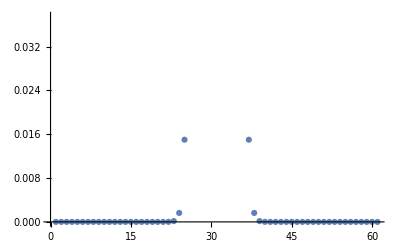

```mathematica
particles = Table[0, 101];
particles[[51]] = 100;
particles
p = 0.1

positions =
Nest[

ListConvolve[
{p/2, (1-p), p/2},
#]&,

particles,

20]

ListPlot[positions]
(** the list is getting shorter and shorter because of listconvolve cutting it **)
```

3. This problem sets up a demonstration of the Rayleigh criterion for the separation of images. The criterion depends on the diffraction pattern of a circular aperture: the intensity in a beam at an angle θ from the normal to an aperture of radius a is
    I(θ)=((2J_1(k a Sin(θ)))/(k a Sin(θ)) )^2 
where k is the wavevector of the light and J_1 is the first order Bessel function of the first kind (BesselJ).
   First create an ideal image. This should be a series of one-unit spikes, at varying spacngs. Create a 255 by 255 grid, with one spike at the centre, and at the corners and  centres of edges of squares, centred on the centre, with edges of lengths 8, 16, 32, 64, 128.
   Now set up a square array, 40 by 40, to represent the blurring arising from this function. Take ka=200, and calculate θ assuming that the image is 2000 units from the aperture, and that the spacing of the mesh is 1 unit. First plot your blur function, then convolve it with the image. 
      Comment on whether your impression of the resulting blurred image is consistent with Rayleigh's criterion, which states that two images can be resolved if their angular separation is greater than 1.22 λ/d where d is the diameter of the aperture and λ is the wavelength.

A.H. Harker
Physics and Astronomy, UCL
January 2008, revised January 2009.